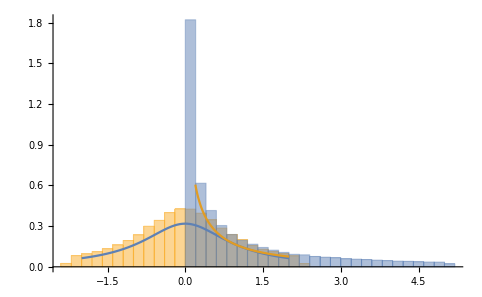

```mathematica
d=ProbabilityDistribution[1/(Pi*(1+x^2)),{x,-2,2}];
rands=RandomVariate[d, 10^5];
Function[x,x^2]/@rands;
Show[Histogram[{rands, %},50, "PDF"], Plot[{PDF[d,x], 1/(Pi(1+x)x^(1/2))}, {x, -2, 2}]]
```

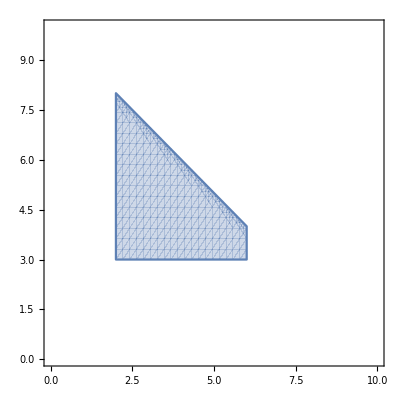

11.9984

```mathematica
a=2;
b=3;
ma=4;
mb=6;
RegionPlot[{x+y<10},{x,ma-a,ma+a},{y,mb-b,mb+b},PlotRange-> {0, 10}]
Area[DiscretizeGraphics[%]]
```

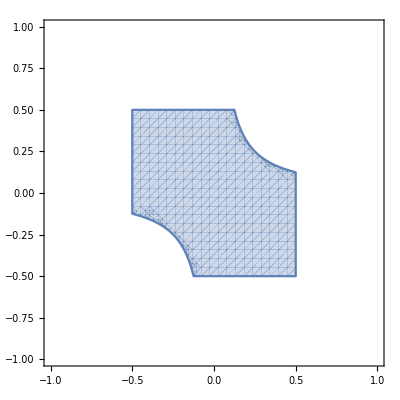

0.798292

```mathematica
RegionPlot[{x*y<1/16},{x,-1/2,1/2},{y,-1/2,1/2}, PlotRange->{-1, 1}]
Area[DiscretizeGraphics[%]]
```

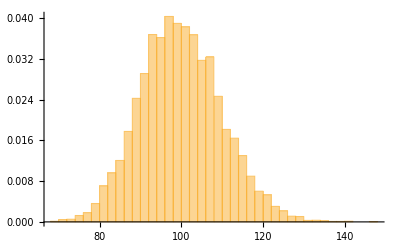

```mathematica
d = ExponentialDistribution[1];
vars = {};
For[i=0, i<10^4, i+=1, AppendTo[vars, Total[RandomVariate[d, 100]]]]
Histogram[{vars},50, "PDF"]
```

```mathematica
AppendTo[vars, Total[RandomVariate[d, 10^10]]]
```

```mathematica
areas = {};
For[i=0, i<10^4, i+=1,
f1=RandomVariate[UniformDistribution[{0, 2*Pi}]];
f2=RandomVariate[UniformDistribution[{0, 2*Pi}]];
AppendTo[areas, Area[DiscretizeGraphics[Graphics[Triangle[{{0, 0}, {Cos[f1], Sin[f1]}, {Cos[f2], Sin[f2]}}]]]]]]
Mean[areas]
```

0.317526

```mathematica
Clear[f1]
Clear[f2]
1/2 NIntegrate[Integrate[(Abs[Sin[f1]]+Abs[Sin[f2-f1]]-Abs[Sin[f2]])/(4*Pi^2), {f2, 0, 2*Pi}], {f1, 0, 2*Pi}]
```

0.31831

```mathematica
Integrate[Abs[x-0.3], {x, 0, 1}]
```

0.29

```mathematica
2*Integrate[(x-0.3), {x, 0.3, 1}]
```

0.49